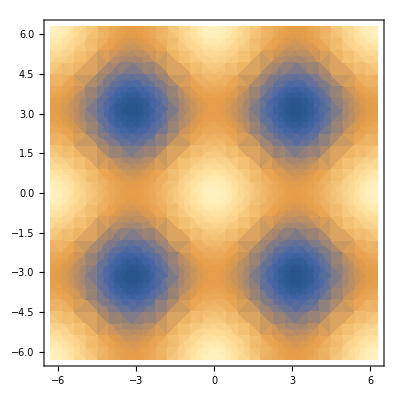

```mathematica
DensityPlot[Cos@x+Cos@y,{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

### The solution here is by fixed boundary condition

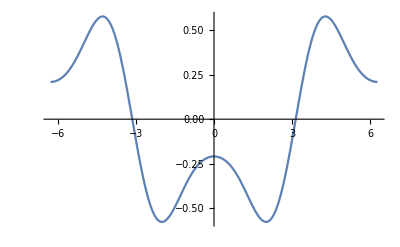

```mathematica
Clear[v,m,e,h2,a]
ϕ[n_,x_]:=1/(√(a π))Sin[(n+1)/(2a) (a π-x)];
H[ω_,a_,m_,n_]:=1/(8 π)(((1+2 n+n^2+8 a^2 ω^2) Sin[(m-n) π])/((m-n) a^2)-((1+2 n+n^2+8 a^2 ω^2) Sin[(2+m+n) π])/((2+m+n) a^2)-4 ω^2 (-Sin[π (m-n-a)]/(m-n-2 a)+Sin[π (2+m+n-a)]/(2+m+n-2 a)+Sin[π a]/(m-n-2 a)-Sin[π a]/(2+m+n-2 a)-Sin[π a]/(m-n+2 a)+Sin[π a]/(2+m+n+2 a)-Sin[π (m-n+a)]/(m-n+2 a)+Sin[π (2+m+n+a)]/(2+m+n+2 a)));ϵ[ω_,β_,i_]:=Eigenvalues[Table[H[ω,β,m+.000001,n],{m,0,4},{n,0,4}]][[i]];
Φ=Table[ϕ[n,x],{n,0,4}];
v[ω_,β_,i_]:=Eigenvectors[Table[H[ω,β,m+.000001,n],{m,0,4},{n,0,4}]][[i]];
ψ[n_,θ_]:=(-1)^(n+1)v[ω,a,5-n].Φ;
a=1;ω=1;
Plot[ψ[0,x],{x,-2a Pi,2a Pi}]
```

```mathematica
V[x_]:=v Cos[2 Pi x/a]/2-v/2;
DSolve[-h2/(2m) f''[x]+V[x]f[x]==e f[x],f[x],x]
```

{{f[x]→C[1] MathieuC[-(a^2 (-2 e m-m v))/(h2 π^2),(a^2 m v)/(2 h2 π^2),(π x)/a]+C[2] MathieuS[-(a^2 (-2 e m-m v))/(h2 π^2),(a^2 m v)/(2 h2 π^2),(π x)/a]}}

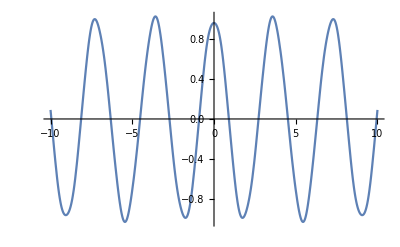

```mathematica
a=1;e=1;m=1;h2=1;v=1;
Plot[ MathieuC[-(a^2 (-2 e m-m v))/(h2 π^2),(a^2 m v)/(2 h2 π^2),(π x)/a],{x,-10,10}]
```

```mathematica
Solve[(a^2 (-2 e m-m v))/(h2 π^2)+MathieuCharacteristicA[0,(a^2 m v)/(2 h2 π^2)]==0,e]
```

{{e→(-a^2 m v+h2 π^2 MathieuCharacteristicA[0,(a^2 m v)/(2 h2 π^2)])/(2 a^2 m)}}